# Chaotic Series

#### Logistic

a_n=4a_(n-1)(1-a_(n-1))

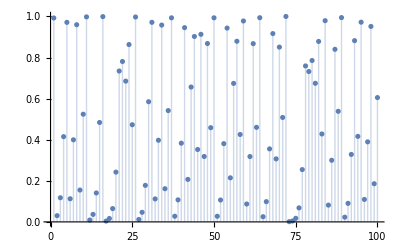

```mathematica
Block[{n=100,a0=RandomReal[]},
Block[{data=Table[0,n]},
data[[1]]=a0;
Do[data[[i]]=4data[[i-1]](1-data[[i-1]]),{i,2,n}];
ListPlot[data,Filling->Axis]]]
```

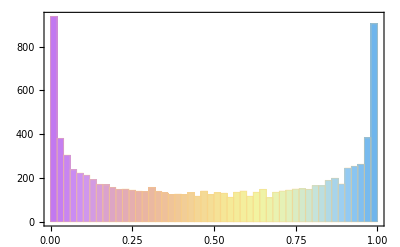

```mathematica
Block[{n=10000,a0=RandomReal[]},
Block[{data=Table[0,n]},
data[[1]]=a0;
Do[data[[i]]=4data[[i-1]](1-data[[i-1]]),{i,2,n}];
Histogram[data,{.02},ChartStyle->"Pastel",Axes->False,Frame->True]]]
```

```mathematica
2
```